```mathematica
ASSIGNMENT - 7

Om Gupta
214047
```

```mathematica
eqn1=x D[u[x,y],x]+y D[u[x,y],y]==u[x,y]+1;
chareq1=DSolve[x y'[x]==y[x],y[x],x]
```

{{y[x]→x C[1]}}

```mathematica
char1=y[x]/. chareq1/. C[1]->{2,3,4}
```

{{2 x,3 x,4 x}}

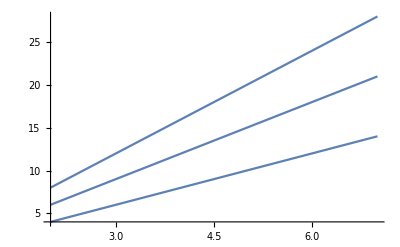

```mathematica
Plot[char1, {x, 2, 7}]
```

```mathematica
eqn2 = 3 D[u[x, y], x] + 2 D[u[x, y], y] == 0;
chareq2 = DSolve[3 y'[x] == 2, y[x], x]
```

{{y[x]→(2 x)/3+C[1]}}

```mathematica
char2 = y[x] /. chareq2 /. C[1] -> {2, 3, 4}
```

{{2+(2 x)/3,3+(2 x)/3,4+(2 x)/3}}

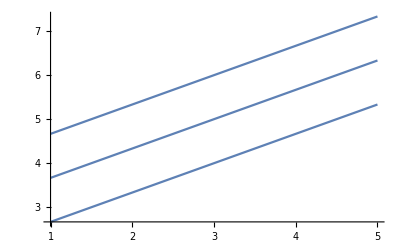

```mathematica
Plot[char2, {x, 1, 5}]
```